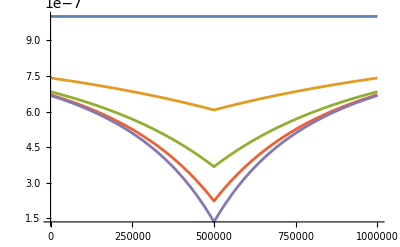

```mathematica
(*probability of deleterious allele at linked site some time t in the past ND13 eq. 2*)
(*using prob. of recombination b/w focal and linked site = r x, x = Abs[Subscript[s, f]-Subscript[s, L]]*)
(*in general, rx, u, s can be any function of the positions of the focal and linked site*)
(*can also include back mutations, see ND13 supplement*)
pMut:=u/s((r x)/(r x + s)+s/(r x + s)ⅇ^(-r x t - s t));
(*ND13 figure 2*)
Table[pMut/.{u->10^-8,r->4 10^-8,s->10^-2,t->τ,x->Abs[x-5 10^5]},{τ,{0,50,100,150,2 10^2}}];
Plot[%,{x,0,10^6}]
```

```mathematica
(*ND13 eq. 3*)
(*solving integral that is in the exponent*)
expExpression = - 2 u/s Integrate[(s/(r x + s)(1-Exp[-r x t - s t]))^2,{x,0,l/2},Assumptions->{r>0,s>0,t>0,l>0}]//Collect[#,ⅇ^_]&//Expand
```

(4 ⅇ^(-s t) l u)/(l r+2 s)+(8 ⅇ^(-s t) s u)/(r (l r+2 s))-(8 ⅇ^(-1/2 l r t-s t) s u)/(r (l r+2 s))-(2 l s u)/(l r s+2 s^2)-(2 ⅇ^(-2 s t) l s u)/(l r s+2 s^2)-(4 ⅇ^(-2 s t) s^2 u)/(r (l r s+2 s^2))+(4 ⅇ^(-l r t-2 s t) s^2 u)/(r (l r s+2 s^2))-(4 s t u Gamma[0,s t])/r+(4 s t u Gamma[0,2 s t])/r+(4 s t u Gamma[0,(l r t)/2+s t])/r-(4 s t u Gamma[0,l r t+2 s t])/r

```mathematica
(*confirming our result matches their expression*)
-2 (u l)/(r l)((1-ⅇ^(-s t))^2-s/(s+r l /2)(1-ⅇ^(- s t- r l t / 2))^2+2s t(Gamma[0,s t,2s t]-Gamma[0,r l t /2 + s t,r l t+2 s t]))==%//FullSimplify
```

True

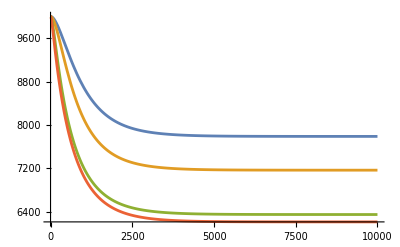

```mathematica
(*approximating the effects of BGS as a time dep. eff. pop size Ne(t)*)
(*ND13 eq. 3*)
(*really a time dependent scaling of the population size given by expExpression*)
(*n here is census size, can be replaced by n(t)*)
ne:=n Exp[expExpression];
(*ND13 fig 3*)
Table[ne/.{u->10^-8,r->4 10^-8,s->10^-3,n->10^4},{l,{5 10^4,10^5,5 10^5,10^6}}];
Plot[%,{t,0,10^4}]
```

```mathematica
(*finding long term equil. Ne*)
```

```mathematica
Limit[ne,t->∞, Assumptions->{l>0,s>0,r>0,u>0,n>0}]
```

ⅇ^(-(2 l u)/(l r+2 s)) n

```mathematica
(*Ne(t) recovers current census size at the present*)
(*but plugging in t=0 is undefined*)
```

```mathematica
Limit[ne,t->0,Assumptions->{l>0,s>0,r>0,u>0,n>0}]
ne/.t->0
```

n

Infinity::indet: Indeterminate expression (0 s u ∞)/r encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Indeterminate

```mathematica
(*result of the t Gamma[0,c t] terms, c = constant*)
(*can probably redifine Times[0,∞] to evaluate to 0 if we care that much*)
{Gamma[0,(l r t)/2+s t]/.t->0,
t Gamma[0,(l r t)/2+s t]/.t->0}
```

Infinity::indet: Indeterminate expression 0 ∞ encountered.

{∞,Indeterminate}

```mathematica
(*in the expressions above time was in generations and backwards in time*)
(*t=0 corresponded to present*)
(*for diffusion we need time to go forward t=0 corresponds to ancestral equil*)
(*and time in genomic units*)
(*need to think about how to automate choosing when to start the diffusion*)
(*how to find when the long term equil is reached*)
```

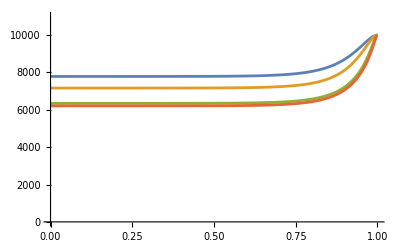

```mathematica
ne=ne/.t-> n t/.t->1-t;
Table[ne/.{u->10^-8,r->4 10^-8,s->10^-3,n->10^4},{l,{5 10^4,10^5,5 10^5,10^6}}];
Plot[%,{t,0,1},PlotRange->{{0,1},{0,11000}}]
```

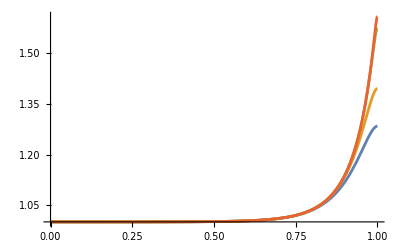

```mathematica
(*for diffusion approx we define v = Ne(t)/Ne(Ancestral)*)
v = ne/(ⅇ^(-(2 l u)/(l r+2 s)) n);
Table[v/.{u->10^-8,r->4 10^-8,s->10^-3,n->10^4},{l,{5 10^4,10^5,5 10^5,10^6}}];
Plot[%,{t,0,1},PlotRange->All]
```

```mathematica
(*ancestral, equilibrium SFS assuming neutrality at focal site*)
equil=θ/x/.θ->4 u (ⅇ^(-(2 l u)/(l r+2 s)) n)
```

(4 ⅇ^(-(2 l u)/(l r+2 s)) n u)/x

```mathematica
(*solving forward in time from this equil using the change of variables from Evansetal07*)
gequil=x(1-x) equil;
nsoln=NDSolve[Evaluate[{D[g[t,x],t]==(x(1-x))/(2 v)D[g[t,x],{x,2}],
g[0,x]==gequil,
g[t,0]==4 ⅇ^(-(2 l u)/(l r+2 s)) n u v (*θ(Ancestral) v*)
}/.{l->10^6,u->10^-8,r->4 10^-8,s->10^-3,n->10^4}],g,{t,0,1-10^-4},{x,0,1},MaxStepSize->0.00025];
```

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

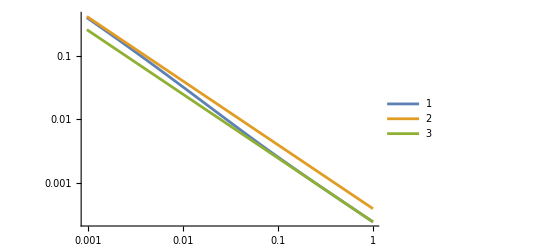

```mathematica
(*plotting against a constant population size*)
LogLogPlot[{g[t,x]/(x(1-x))/.nsoln/.t->1-10^-4,(*time dep BGS apprx.*)
4 n u /x/.{n->10^4,u->10^-8}, (*pop size is census size*)
4 ⅇ^(-(2 l u)/(l r+2 s)) n u/x/.{l->10^6,u->10^-8,r->4 10^-8,s->10^-3,n->10^4} (*pop size is long term limit with BGS*)
},{x,0,1},PlotRange->All,PlotLegends->Automatic]
```

```mathematica
(*one region of size l, located l away from the focal site uniform map*)
```

```mathematica
Integrate[u/s(s/(r x + s)(1-ⅇ^(-t(r x +s))))^2,{x,l,2l},Assumptions->{r>0,s>0,t>0,l>0}]
```

(s u (ⅇ^(-2 (l r+s) t)/(l r+s)-(2 ⅇ^(-((l r+s) t)))/(l r+s)-ⅇ^(-2 (2 l r+s) t)/(2 l r+s)+(2 ⅇ^(-((2 l r+s) t)))/(2 l r+s)+(l r)/((l r+s) (2 l r+s))+2 t Gamma[0,(l r+s) t]-2 t Gamma[0,2 (l r+s) t]-2 t Gamma[0,(2 l r+s) t]+2 t Gamma[0,2 (2 l r+s) t]))/r

```mathematica
(*replacing the one region with a point mass, distance from focal site to region midpoint is 3/2 l, scaling up mutation rate*)
u/s(s/(r x + s)(1-ⅇ^(-t(r x +s))))^2/.{u -> l u,x->3/2 l}
```

((1-ⅇ^(-(((3 l r)/2+s) t)))^2 l s u)/((3 l r)/2+s)^2

```mathematica
Manipulate[Plot[{Exp[-%]/.{l->regionSize,u->10^-8,r->4 10^-8,s->10^-3,n->10^4},
Exp[-%%]/.{l->regionSize,u->10^-8,r->4 10^-8,s->10^-3,n->10^4}},{t,0,10^4},PlotRange->All,PlotLegends->Automatic],{regionSize,0,10^5}]
```

```mathematica
(*extending to a 1 Mb region with many point masses*)
```

```mathematica
(*ND13 eq. 3*)
(*solving integral that is in the exponent*)
exactExp=- 2 u/s Integrate[(s/(r x + s)(1-Exp[-r x t - s t]))^2,{x,0,l/2},Assumptions->{r>0,s>0,t>0,l>0}];
```

```mathematica
(*approximating as 100 equally spaced point masses*)
Table[i,{i,5 10^3,99.5 10^4,10^4}];
approxExp=Total[Table[-u/s(s/(r x + s)(1-ⅇ^(-t(r x +s))))^2/.{u -> 10^4 u,x->Abs[x-5 10^5]},{x,%14}]];
```

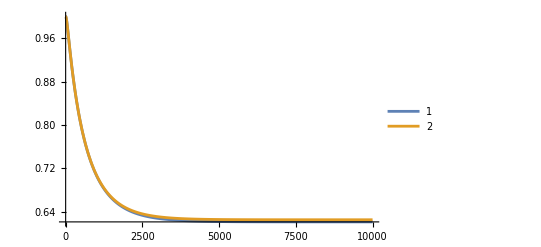

```mathematica
Plot[{Exp[exactExp]/.{l->10^6,u->10^-8,r->4 10^-8,s->10^-3,n->10^4},
Exp[approxExp]/.{u->10^-8,r->4 10^-8,s->10^-3,n->10^4}},{t,0,10^4},PlotRange->All,PlotLegends->Automatic]
```

```mathematica
(*one region that is split by a hotspot*)
```

```mathematica
Integrate[u/s(s/(r x +10^-5 Boole[x>2 10^4] + s)(1-ⅇ^(-t(r x +10^-5 Boole[x>2 10^4] +s))))^2,{x,10^4,3 10^4},Assumptions->{r>0,s>0,t>0,l>0}];
```

```mathematica
(*replacing the region with 2 point masses*)
Total[Table[u/s(s/(r x +10^-5 Boole[x>2 10^4] + s)(1-ⅇ^(-t(r x +10^-5 Boole[x>2 10^4] +s))))^2,{x,{1.5 10^4,2.5 10^4}}]]/.u->10^4 u
```

(10000 (1-ⅇ^(-((15000. r+s) t)))^2 s u)/(15000. r+s)^2+(10000 (1-ⅇ^(-((1/100000+25000. r+s) t)))^2 s u)/(1/100000+25000. r+s)^2

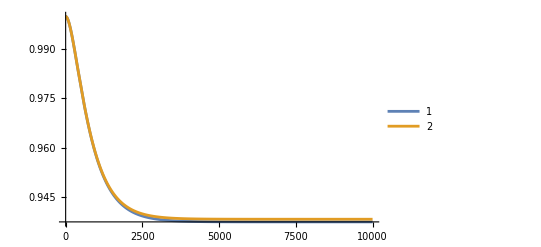

```mathematica
Plot[{Exp[-%37]/.{u->10^-8,r->4 10^-8,s->10^-3,n->10^4},Exp[-%38]/.{u->10^-8,r->4 10^-8,s->10^-3,n->10^4}},{t,0,10^4},PlotRange->All,PlotLegends->Automatic]
```

```mathematica
expExression[Subscript[x, i],Subscript[x, f],t]:=u[Subscript[x, i]]/s[Subscript[x, i]](s[Subscript[x, i]]/(r[Subscript[x, i],Subscript[x, f]]+s[Subscript[x, i]])(1-ⅇ^(-t(r[Subscript[x, i],Subscript[x, f]]+s[Subscript[x, i]]))))^2
```